```mathematica
nsubst = {ϵ2->1/2 (√(4 Δ^2+λ^2+4 Δ λ nz)-λ),ϵ1->1/2 (λ+√(4 Δ^2+λ^2-4 Δ λ nz)),μ->10,Δ->0.1,λ->0.25,nz->.9,β->20}
expr = Integrate[1/π((μ-ϵ) (ϵ/2+λ/4)),{ϵ,ϵ2,ϵ1}] + Integrate[1/π((μ-ϵ) ϵ),{ϵ,ϵ1,μ}]//Simplify//Expand//FullSimplify;
expr = -expr;
%//.nsubst
NIntegrate[1/(π β)Log[1+Exp[β(μ-ϵ)]] (ϵ/2+λ/4)//.nsubst,{ϵ,ϵ2//.nsubst,ϵ1//.nsubst}]+NIntegrate[1/(π β)Log[1+Exp[β(μ-ϵ)]] ϵ//.nsubst,{ϵ,ϵ1//.nsubst,μ//.nsubst}];
-%
```

{ϵ2→1/2 (√(4 Δ^2+λ^2+4 Δ λ nz)-λ),ϵ1→1/2 (λ+√(4 Δ^2+λ^2-4 Δ λ nz)),μ→10,Δ→0.1,λ→0.25,nz→0.9,β→20}

-53.0359

-53.0424

### Density of States

Piecewise[{{0, 0<ϵ<1/2 (√(0.1 nz+0.1025)-0.25)}, {ϵ/2+0.0625, 1/2 (√(0.1 nz+0.1025)-0.25)<ϵ<1/2 (√(0.1025-0.1 nz)+0.25)}, {ϵ, ϵ>1/2 (√(0.1025-0.1 nz)+0.25)}}]

Piecewise[{{0, 0<ϵ<1/2 (√(0.1025-0.1 nz)-0.25)}, {ϵ/2+0.0625, 1/2 (√(0.1025-0.1 nz)-0.25)<ϵ<1/2 (√(0.1 nz+0.1025)+0.25)}, {ϵ, ϵ>1/2 (√(0.1 nz+0.1025)+0.25)}}]

Piecewise[{{0, 0<ϵ<0.1}, {ϵ/2+0.0625, 0.1<ϵ<0.15}, {ϵ, ϵ>0.15}}]

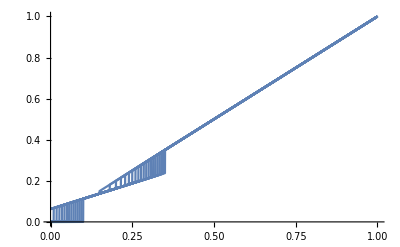

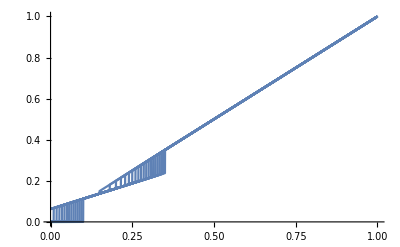

```mathematica
nsubst1={ϵ2->1/2 (√(4 Δ^2+λ^2+4 Δ λ nz)-λ),ϵ1->1/2 (λ+√(4 Δ^2+λ^2-4 Δ λ nz)),Δ->0.1,λ->0.25,μ->5,β->20};
nsubst2={ϵ2->1/2 (√(4 Δ^2+λ^2-4 Δ λ nz)-λ),ϵ1->1/2 (λ+√(4 Δ^2+λ^2+4 Δ λ nz)),Δ->0.1,λ->0.25,μ->5,β->20};
Clear[i1,i2];
i1[nz_] = Piecewise[{{0,0<ϵ<ϵ2},{(ϵ/2+λ/4),ϵ2<ϵ<ϵ1},{ ϵ,ϵ>ϵ1}}]//.nsubst1
i2[nz_]= Piecewise[{{0,0<ϵ<ϵ2},{ (ϵ/2+λ/4),ϵ2<ϵ<ϵ1},{ ϵ,ϵ>ϵ1}}]//.nsubst2
i1[1]
Plot[Table[i1[i],{i,-1,1,0.1}],{ϵ,0,1}]
Plot[Table[i2[i],{i,-1,1,0.1}],{ϵ,0,1}]
```

```mathematica
bigexpr = expr/.{ϵ2->1/2 (√(4 Δ^2+λ^2+4 Δ λ nz)-λ),ϵ1->1/2 (λ+√(4 Δ^2+λ^2-4 Δ λ nz))}//Simplify
bigexpr = bigexpr+(bigexpr/.nz->-nz);
```

-(8 μ^3+4 Δ^2 (-6 μ+√(4 Δ^2+λ^2-4 Δ λ nz)+√(4 Δ^2+λ^2+4 Δ λ nz))-4 Δ λ nz (3 λ+√(4 Δ^2+λ^2-4 Δ λ nz)-√(4 Δ^2+λ^2+4 Δ λ nz))+λ^2 √(4 Δ^2+λ^2-4 Δ λ nz)+λ^2 √(4 Δ^2+λ^2+4 Δ λ nz))/(48 π)

### Numerical Checks Ω

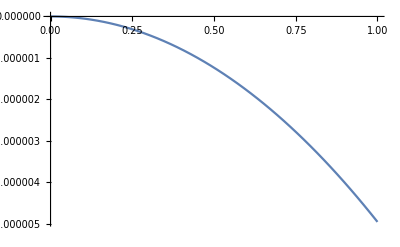

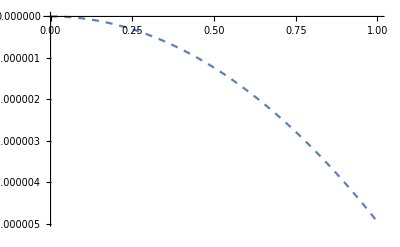

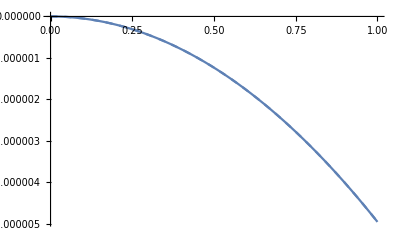

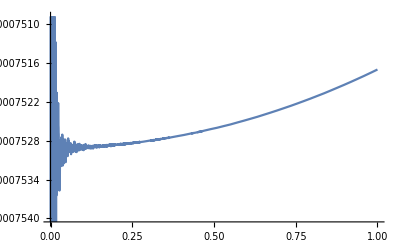

```mathematica
NΩ[nz_,Δ_,λ_,μ_,β_] := Block[{tmp1,tmp2,ϵ11,ϵ12,ϵ21,ϵ22},
	ϵ21=1/2 (√(4 Δ^2+λ^2+4 Δ λ nz)-λ);
	ϵ22=1/2 (√(4 Δ^2+λ^2-4 Δ λ nz)-λ);
	ϵ11= 1/2 (λ+√(4 Δ^2+λ^2-4 Δ λ nz));
	ϵ12 = 1/2 (λ+√(4 Δ^2+λ^2+4 Δ λ nz));
	;
	;
	tmp1 =  NIntegrate[1/(π β)Log[1+Exp[β(μ-ϵ)]] (ϵ/2+λ/4),{ϵ,ϵ21,ϵ11}]+NIntegrate[1/(π β)Log[1+Exp[β(μ-ϵ)]] ϵ,{ϵ,ϵ11,μ}];
	tmp2 =  NIntegrate[1/(π β)Log[1+Exp[β(μ-ϵ)]] (ϵ/2+λ/4),{ϵ,ϵ22,ϵ12}]+NIntegrate[1/(π β)Log[1+Exp[β(μ-ϵ)]] ϵ,{ϵ,ϵ12,μ}];
	-(tmp1+tmp2)
]
Ω[nz_,Δ_,λ_,μ_]=bigexpr;

Plot[Ω[x,0.1,0.025,2]    -Ω[0,0.1,0.025,2],{x,0,1}]
Plot[NΩ[x,0.1,0.025,2,20]-NΩ[0,0.1,0.025,2,20],{x,0,1},PlotStyle->Dashed]
Show[%,%%]
Plot[(NΩ[x,0.1,0.025,2,5]-NΩ[0,0.1,0.025,2,5]-
             Ω[x,0.1,0.025,2]+Ω[0,0.1,0.025,2])/(NΩ[x,0.1,0.025,2,5]-NΩ[0,0.1,0.025,2,5]),{x,0,1}]
```

### Phase Diagram

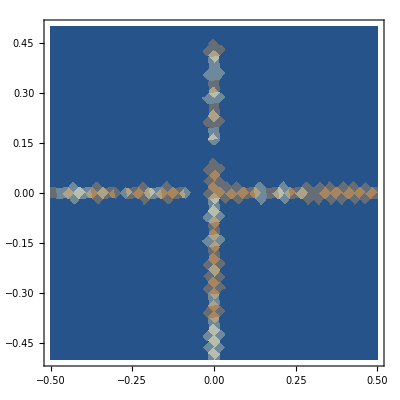

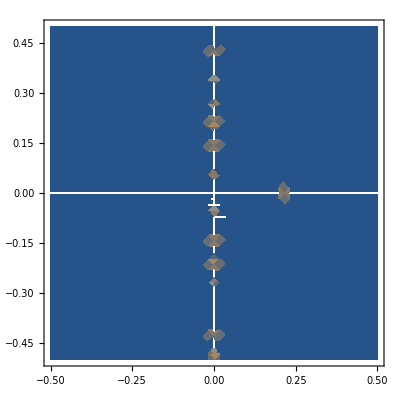

```mathematica
k[x_,y_]:= Sign[NΩ[1,x,y,2,20]-NΩ[0,x,y,2,20]]
kp[x_,y_]:= Sign[Ω[1,x,y,2]-Ω[0,x,y,2]]

DensityPlot[k[x,y],{x,-0.5,0.5},{y,-0.5,0.5}]
DensityPlot[kp[x,y],{x,-0.5,0.5},{y,-0.5,0.5}]
```

-(8 μ^3+4 Δ^2 (-6 μ+√(4 Δ^2+λ^2-2 Δ λ (x^2-2))+√(4 Δ^2+λ^2+2 Δ λ (x^2-2)))-2 Δ λ (x^2-2) (√(4 Δ^2+λ^2-2 Δ λ (x^2-2))-√(4 Δ^2+λ^2+2 Δ λ (x^2-2)))+λ^2 (√(4 Δ^2+λ^2-2 Δ λ (x^2-2))+√(4 Δ^2+λ^2+2 Δ λ (x^2-2))))/(24 π)

(-4 Δ^2 Abs[2 Δ-λ]-4 Δ^2 Abs[2 Δ+λ]-λ^2 Abs[2 Δ-λ]-λ^2 Abs[2 Δ+λ]+4 Δ λ Abs[2 Δ-λ]-4 Δ λ Abs[2 Δ+λ]+24 Δ^2 μ-8 μ^3)/(24 π)+(x^2 (4 Δ^3 λ Abs[2 Δ-λ]-4 Δ^3 λ Abs[2 Δ+λ]+4 Δ^2 λ^2 Abs[2 Δ-λ]+4 Δ^2 λ^2 Abs[2 Δ+λ]+Δ λ^3 Abs[2 Δ-λ]-Δ λ^3 Abs[2 Δ+λ]+2 Δ λ Abs[2 Δ-λ] Abs[2 Δ+λ]^2-2 Δ λ Abs[2 Δ-λ]^2 Abs[2 Δ+λ]))/(24 π Abs[2 Δ-λ] Abs[2 Δ+λ])

(Δ λ (-2 Abs[2 Δ-λ]+2 Abs[2 Δ+λ]+(λ-2 Δ) 2 Δ-λ+(2 Δ+λ) 2 Δ+λ))/(24 π)

-(4 Δ^2 (√(4 Δ^2-4 Δ λ+λ^2)+√(4 Δ^2+4 Δ λ+λ^2))+4 Δ λ (√(4 Δ^2+4 Δ λ+λ^2)-√(4 Δ^2-4 Δ λ+λ^2))+λ^2 (√(4 Δ^2-4 Δ λ+λ^2)+√(4 Δ^2+4 Δ λ+λ^2)))/(24 π)

-(4 Δ^2 (√(4 Δ^2-3.98 Δ λ+λ^2)+√(4 Δ^2+3.98 Δ λ+λ^2))+3.98 Δ λ (√(4 Δ^2+3.98 Δ λ+λ^2)-√(4 Δ^2-3.98 Δ λ+λ^2))+λ^2 (√(4 Δ^2-3.98 Δ λ+λ^2)+√(4 Δ^2+3.98 Δ λ+λ^2)))/(24 π)

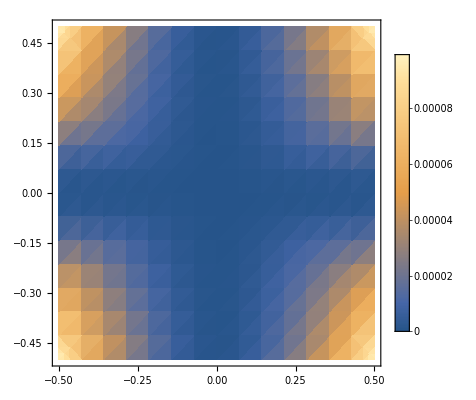

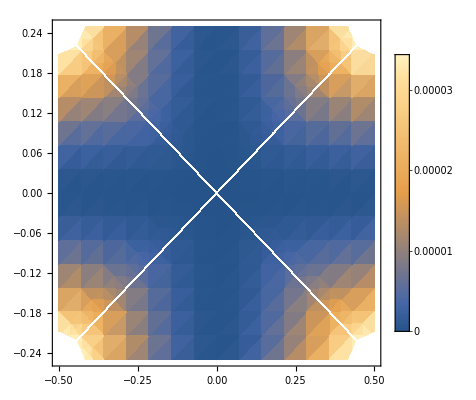

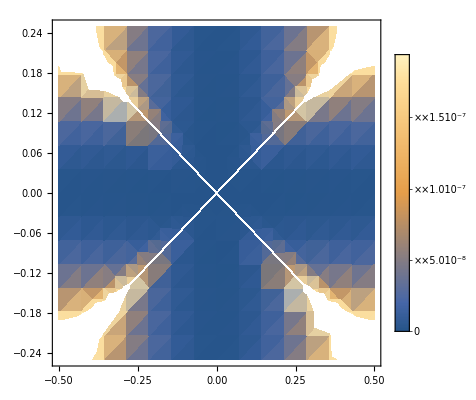

```mathematica
ExprExact=Ω[1-x^2/2,Δ, λ,μ]//Simplify
ExprApprox1=%/.{√(4 Δ^2+λ^2-2 Δ λ (x^2-2))->Abs[2Δ+λ]-(Δ λ x^2)/Abs[2Δ+λ],√(4 Δ^2+λ^2+2 Δ λ (x^2-2))->Abs[2Δ-λ]+(Δ λ x^2)/Abs[2Δ-λ]}//Series[#,{x,0,2}]&//Normal
ExprApprox2 = Coefficient[%,x,2]//FullSimplify
ExprApproxMisha = Ω[nz,Δ, λ,μ]//Series[#,{nz,0,2}]&//Normal;

ExprExact/.x->0/.μ->0
ExprExact/.{x->0.1,μ->0}
x1=%-%%;x1//DensityPlot[#,{λ,-0.5,0.5},{Δ,-0.5,0.5},PlotLegends->True]&

x2=ExprApprox2 0.1^2/.μ->0;x2 //DensityPlot[#,{λ,-0.5,0.5},{Δ,-0.25,0.25},PlotLegends->True]&

(x2-x1)//DensityPlot[#,{λ,-0.5,0.5},{Δ,-0.25,0.25},PlotLegends->True]&
```

```mathematica
cases = {
	{Δ>0, λ>0,Abs[2Δ] <Abs[λ]},
	{Δ>0, λ<0,Abs[2Δ ]<Abs[λ]},
	{Δ<0, λ>0,Abs[2Δ ]<Abs[λ]},
	{Δ<0, λ<0,Abs[2Δ ]<Abs[λ]},
	{Δ>0, λ>0,Abs[2Δ] >Abs[λ]},
	{Δ>0, λ<0,Abs[2Δ ]>Abs[λ]},
	{Δ<0, λ>0,Abs[2Δ ]>Abs[λ]},
	{Δ<0, λ<0,Abs[2Δ ]>Abs[λ]}
};

Table[{case, FullSimplify[ExprApprox2,case]},{case,cases}]
```

({Δ>0,λ>0,2 Abs[Δ]<Abs[λ]} | (Δ^2 λ)/(2 π)
{Δ>0,λ<0,2 Abs[Δ]<Abs[λ]} | -(Δ^2 λ)/(2 π)
{Δ<0,λ>0,2 Abs[Δ]<Abs[λ]} | (Δ^2 λ)/(2 π)
{Δ<0,λ<0,2 Abs[Δ]<Abs[λ]} | -(Δ^2 λ)/(2 π)
{Δ>0,λ>0,2 Abs[Δ]>Abs[λ]} | (Δ λ^2)/(4 π)
{Δ>0,λ<0,2 Abs[Δ]>Abs[λ]} | (Δ λ^2)/(4 π)
{Δ<0,λ>0,2 Abs[Δ]>Abs[λ]} | -(Δ λ^2)/(4 π)
{Δ<0,λ<0,2 Abs[Δ]>Abs[λ]} | -(Δ λ^2)/(4 π))

```mathematica
0.1,0.025
```

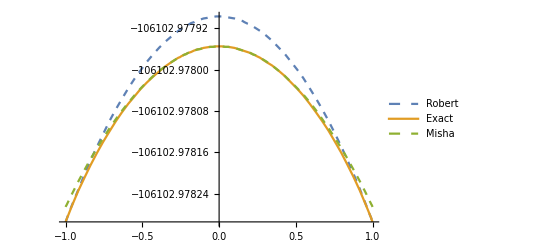

```mathematica
Plot[Evaluate@({ExprApprox1,bigexpr, ExprApproxMisha}/.{Δ->0.1,λ->0.25,x^2->1-nz^2,μ->100}),{nz,-1,1}, PlotLegends->{"Robert", "Exact", "Misha"}, PlotStyle->{{Thick,Dashed}, {Thick,Automatic},{Thick,Dashed}}]
```

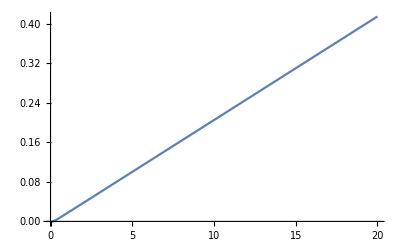

```mathematica
Plot[{Ω[0,0.1,0.25,μ]-NΩ[0,0.1,0.25,μ,5]},{μ,0,20}]
```

```mathematica
bigexpr
```

-(8 μ^3+4 Δ^2 (-6 μ+√(4 Δ^2+λ^2-4 Δ λ nz)+√(4 Δ^2+λ^2+4 Δ λ nz))-4 Δ λ nz (3 λ+√(4 Δ^2+λ^2-4 Δ λ nz)-√(4 Δ^2+λ^2+4 Δ λ nz))+λ^2 √(4 Δ^2+λ^2-4 Δ λ nz)+λ^2 √(4 Δ^2+λ^2+4 Δ λ nz))/(48 π)-(8 μ^3+4 Δ^2 (-6 μ+√(4 Δ^2+λ^2-4 Δ λ nz)+√(4 Δ^2+λ^2+4 Δ λ nz))+4 Δ λ nz (3 λ-√(4 Δ^2+λ^2-4 Δ λ nz)+√(4 Δ^2+λ^2+4 Δ λ nz))+λ^2 √(4 Δ^2+λ^2-4 Δ λ nz)+λ^2 √(4 Δ^2+λ^2+4 Δ λ nz))/(48 π)

```mathematica
n = {nx Exp[ⅈ ω t],ny Exp[ⅈ ω t],1};m={mx Exp[ⅈ ω t],my Exp[ⅈ ω t],0};nperp={0,0,1};
Clear[Ω];
Join[Ω n×m -K m× nperp+αm n× D[m,t] +h n× {0,0,1},-K n × nperp+αm m × D[m,t]+h m × {0,0,1}]/.{my nx->0, mx ny->0,t->0}
%-ⅈ ω  {nx,ny,0,mx,my,0}
%[[{1,2,4,5}]]
(%//CoefficientArrays[#,{nx,ny,mx,my}]&)[[2]]//Normal
ω /.Solve[Det[%]==0, ω]/.h->0//FullSimplify[#,{Ω>0,K>0}]&
%/.αm->0//Simplify
```

{h ny-K my-ⅈ αm my ω-my Ω,-h nx+K mx+ⅈ αm mx ω+mx Ω,0,h my-K ny,K nx-h mx,0}

{h ny-K my-ⅈ αm my ω-my Ω-ⅈ nx ω,-h nx+K mx+ⅈ αm mx ω+mx Ω-ⅈ ny ω,0,h my-K ny-ⅈ mx ω,-h mx+K nx-ⅈ my ω,0}

{h ny-K my-ⅈ αm my ω-my Ω-ⅈ nx ω,-h nx+K mx+ⅈ αm mx ω+mx Ω-ⅈ ny ω,h my-K ny-ⅈ mx ω,-h mx+K nx-ⅈ my ω}

(-ⅈ ω | h | 0 | -K-ⅈ αm ω-Ω
-h | -ⅈ ω | K+ⅈ αm ω+Ω | 0
0 | -K | -ⅈ ω | h
K | 0 | -h | -ⅈ ω)

{1/2 (-√(K (4 Ω-(αm^2-4) K))+ⅈ αm K),1/2 (√(K (4 Ω-(αm^2-4) K))+ⅈ αm K),1/2 (-√(K (4 Ω-(αm^2-4) K))+ⅈ αm K),1/2 (√(K (4 Ω-(αm^2-4) K))+ⅈ αm K)}

{-√(K (K+Ω)),√(K (K+Ω)),-√(K (K+Ω)),√(K (K+Ω))}